# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

生ログ用

オリジナルを”/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231120/T=4/_story/”とする。
実行結果が妥当かは上記と比較する。

Rev: ディレクトリ名の変更

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.93451684990216×10^9

#### 変数

```mathematica
date="20231120"
```

20231120

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci"
base["cs"]="T=cs"
base["la"]="T=la"
base["wk"]="T=wk"
base["all"]="T=4"
```

T=ci

T=cs

T=la

T=wk

T=4

```mathematica
mountdir="/Volumes/home/NII/togo-log/rcoslogs/"
```

/Volumes/home/NII/togo-log/rcoslogs/

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20231120.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20231120.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

22645372 320069013 10381193889 log-20231120.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## リンク(4)

### データ(ci)

```mathematica
dir["ci"]=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=ci

#### データの読み込み

```mathematica
file["ci"]="self.1"
```

self.1

```mathematica
str["ci"]=Import[dir["ci"]<>"/"<>file["ci"],"String"];
```

```mathematica
(strSplt["ci"]=StringSplit[str["ci"],"\n"])//Length
```

2557038

```mathematica
(strSplt1["ci"]=Map[StringSplit[#,"\t"]&,strSplt["ci"]])//Dimensions
```

{2557038,15}

#### カラムポジションの調整

不要。

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1C["ci"]=Map[ReplacePart[#,8->"https://cir.nii.ac.jp/"<>StringDrop[#[[8]],8]]&,strSplt1["ci"]];
```

レファラーのキーを削除する。

```mathematica
strSplt1CC["ci"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["ci"]];
```

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["ci"][s_String]:=AbsoluteTime[DateList[StringTake[s,{8,-6}]]]
```

```mathematica
logdateToTime["ci"][strSplt1CC["ci"][[1]][[6]]]
```

3.90943×10^9

```mathematica
strSplt1CCC["ci"]=Map[ReplacePart[#,6->logdateToTime["ci"][#[[6]]]]&,strSplt1CC["ci"]];
```

remoteをアドレスのみに。

```mathematica
ip["ci"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCCpre["ci"]=Map[ReplacePart[#,3->ip["ci"][#[[3]]]]&,strSplt1CCC["ci"]];
```

```mathematica
strSplt1CCCCpre["ci"][[10]]//TableForm
```

2023-11-19T15:00:01Z
log.ci0001.aws.wa03.yobi
35.216.53.137
host":"-
user":"-
3.90943×10^9
method":"GET
https://cir.nii.ac.jp/all?q=%E4%BA%95%E4%B8%8A%E5%93%B2%E6%AC%A1%E9%83%8E
code":"200
size":"17876
https://cir.nii.ac.jp/crid/1020282257445677312
agent":"Mozilla/5.0 (Windows NT 10.0; Win64; x64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/119.0.0.0 Safari/537.36
http_x_forwarded_for":"\"35.216.53.137\"
request_time":"0.229
upstream_response_time":"0.229"}

pathのCRID、refererのCRIDを追加。

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
strSplt1CCCC["ci"]=Map[Join[#,{toCRID[#[[8]]],toCRID[#[[11]]]}]&,strSplt1CCCCpre["ci"]];
```

StringTake::take: Cannot take positions 1 through 19 in "wp-login.php".

StringTake::take: Cannot take positions 1 through 19 in "ajax-loader.gif".

StringTake::take: Cannot take positions 1 through 19 in "wp-login.php".

General::stop: Further output of StringTake::take will be suppressed during this calculation.

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

Part::partw: Part 5 of {https:,,cir.nii.ac.jp,crid} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{https:,,cir.nii.ac.jp,crid}⟦5⟧,19].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

```mathematica
strSplt1CCCC["ci"][[8]]//TableForm
```

2023-11-19T15:00:01Z
log.ci0001.aws.wa03.yobi
66.249.71.32
host":"-
user":"-
3.90943×10^9
method":"GET
https://cir.nii.ac.jp/crid/1361981470279206912
code":"200
size":"13350
-
agent":"Mozilla/5.0 (compatible; Googlebot/2.1; +http://www.google.com/bot.html)
http_x_forwarded_for":"\"66.249.71.32\"
request_time":"0.032
upstream_response_time":"0.032"}
1361981470279206912
toCRID[-]

```mathematica
accessTime["ci"]=Map[#[[6]]&,strSplt1CCCC["ci"]];
```

### データ(cs)

```mathematica
dir["cs"]=mountdir<>"log/D="<>date<>"/"<>base["cs"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=cs

#### データの読み込み

```mathematica
file["cs"]="self.1"
```

self.1

```mathematica
str["cs"]=Import[dir["cs"]<>"/"<>file["cs"],"String"];
```

```mathematica
(strSplt["cs"]=StringSplit[str["cs"],"\n"])//Length
```

17557

```mathematica
(strSplt1["cs"]=Map[StringSplit[#,"\t"]&,strSplt["cs"]])//Dimensions
```

{17557,14}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 5
4: <- 4
5: <- 6
6: date <- 3
7: <- 7
8: path <- 9
9: <- 8
10: <- 10
11: ref <- 12
12: agent <- 13
13: <- 11
14: <- 14

```mathematica
rp["cs"]={1,2,5,4,6,3,7,9,8,10,12,13,11,14}
```

{1,2,5,4,6,3,7,9,8,10,12,13,11,14}

```mathematica
(strSplt1R["cs"]=Map[#[[rp["cs"]]]&,strSplt1["cs"]])//Dimensions
```

{17557,14}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1R["cs"][[1]][[8]]
```

path":"google.com:443

```mathematica
pathhead["cs"]="https://jupyter.cs.rcos.nii.ac.jp"
```

https://jupyter.cs.rcos.nii.ac.jp

```mathematica
pathreplace["cs"][path_]:=Module[{pathhead,epath},
pathhead="https://jupyter.cs.rcos.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["cs"]=Map[ReplacePart[#,8->pathreplace["cs"][#[[8]]]]&,strSplt1R["cs"]];
```

StringTake::take: Cannot take positions 1 through 1 in "".

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["cs"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["cs"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["cs"][s_String]:=AbsoluteTime[DateList[StringTake[s,{16,-7}]]]
```

```mathematica
strSplt1CC["cs"][[1]][[6]]
```

{"time_local":"2023-11-20T00:08:03.550991834+09:00

```mathematica
strSplt1CCC["cs"]=Map[ReplacePart[#,6->logdateToTime["cs"][#[[6]]]]&,strSplt1CC["cs"]];
```

remoteをアドレスのみに。

```mathematica
ip["cs"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["cs"]=Map[ReplacePart[#,3->ip["cs"][#[[3]]]]&,strSplt1CCC["cs"]];
```

```mathematica
strSplt1CCCC["cs"][[10]]//TableForm
```

2023-11-19T15:16:45Z
log.cs0002.ksw.wa01.yobi
60.120.192.241
stream":"stdout
user":"-
3.90943×10^9
date_time":"19/Nov/2023:15:16:45 +0000
https://jupyter.cs.rcos.nii.ac.jp/user/k251844@kansai-u.ac.jp/jaehyunsong-binder_r-6grbmxkw/rstudio/events/get_events
method":"POST
code":"200
https://jupyter.cs.rcos.nii.ac.jp/user/k251844@kansai-u.ac.jp/jaehyunsong-binder_r-6grbmxkw/rstudio/
agent":"Mozilla/5.0 (Windows NT 10.0; Win64; x64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/119.0.0.0 Safari/537.36
size":"19981
hostname":"fluentd-bllnp"}

```mathematica
accessTime["cs"]=Map[#[[6]]&,strSplt1CCCC["cs"]];
```

### データ(la)

```mathematica
dir["la"]=mountdir<>"log/D="<>date<>"/"<>base["la"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=la

laのログに関し23・9中頃よりsession_idが入る。(12 カラム目 -> 10 カラム目)

#### データの読み込み

```mathematica
file["la"]="self.1"
```

self.1

```mathematica
str["la","pre"]=Import[dir["la"]<>"/"<>file["la"],"String"];
```

```mathematica
(strSplt["la","pre"]=StringSplit[str["la","pre"],"\n"])//Length
```

6254

```mathematica
(strSplt1["la","pre"]=Map[StringSplit[#,"\t"]&,strSplt["la","pre"]])//Dimensions
```

{6254,12}

```mathematica
Map[#[[2]]&,strSplt1["la","pre"]]//Tally
```

{{log.la0001.aws.wa01.yobi,5830},{log.la0003.aws.wa01.yobi,424}}

"log.la0001.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0001.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0001.aws.wa01.yobi"&])//Dimensions
```

{5830,12}

"log.la0002.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0002.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0002.aws.wa01.yobi"&])//Dimensions
```

{0}

"log.la0003.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0003.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0003.aws.wa01.yobi"&])//Dimensions
```

{424,12}

#### カラムポジションの調整

"log.la0001.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0001.aws.wa01.yobi"][[1]]//TableForm
```

2023-11-19T15:00:23Z
log.la0001.aws.wa01.yobi
{"user":"-
date_time":"20/Nov/2023:00:00:23 +0900
method":"GET
path":"/favicon.ico
code":"404
size":"196
referer":"-
agent":"Mozilla/5.0 (Windows NT 10.0; WOW64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/75.0.3770.100 Safari/537.36
http_x_forwarded_for":"122.25.240.254
session_id":"-"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0001.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0001.aws.wa01.yobi"]=Map[#[[rp["la","log.la0001.aws.wa01.yobi"]]]&,strSplt1["la","log.la0001.aws.wa01.yobi"]])//Dimensions
```

{5830,12}

"log.la0002.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0002.aws.wa01.yobi"][[1]]//TableForm
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0002.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0002.aws.wa01.yobi"]=Map[#[[rp["la","log.la0002.aws.wa01.yobi"]]]&,strSplt1["la","log.la0002.aws.wa01.yobi"]])//Dimensions
```

{0}

"log.la0003.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0003.aws.wa01.yobi"][[1]]//TableForm
```

2023-11-20T03:43:20Z
log.la0003.aws.wa01.yobi
{"user":"-
date_time":"20/Nov/2023:03:43:20 +0000
method":"GET
path":"/
code":"302
size":"-
referer":"-
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/119.0.0.0 Safari/537.36
http_x_forwarded_for":"219.113.172.177
session_id":"0760167576e146fca691f134bfe3b2b5"}

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0003.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0003.aws.wa01.yobi"]=Map[#[[rp["la","log.la0003.aws.wa01.yobi"]]]&,strSplt1["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{424,12}

3サービスをマージ

```mathematica
(strSplt1R["la"]=Join[strSplt1R["la","log.la0001.aws.wa01.yobi"],strSplt1R["la","log.la0002.aws.wa01.yobi"],strSplt1R["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{6254,12}

```mathematica
strSplt1R["la"][[1]]
```

{2023-11-19T15:00:23Z,log.la0001.aws.wa01.yobi,http_x_forwarded_for":"122.25.240.254,size":"196,method":"GET,date_time":"20/Nov/2023:00:00:23 +0900,code":"404,path":"/favicon.ico,{"user":"-,session_id":"-"},referer":"-,agent":"Mozilla/5.0 (Windows NT 10.0; WOW64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/75.0.3770.100 Safari/537.36}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["la"]="https://lms.nii.ac.jp"
```

https://lms.nii.ac.jp

```mathematica
pathreplace["la"][path_]:=Module[{pathhead,epath},
pathhead="https://lms.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["la"]=Map[ReplacePart[#,8->pathreplace["la"][#[[8]]]]&,strSplt1R["la"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["la"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["la"]];
```

時刻をMathematica標準にする。

```mathematica
(*logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)*)
```

```mathematica
logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]
```

```mathematica
StringTake[strSplt1CC["la"][[1]][[6]],{13,-6}]//DateList//AbsoluteTime
```

3.90943×10^9

```mathematica
strSplt1CCC["la"]=Map[ReplacePart[#,6->logdateToTime["la"][#[[6]]]]&,strSplt1CC["la"]];
```

```mathematica
strSplt1CCC["la"][[1]]//TableForm
```

2023-11-19T15:00:23Z
log.la0001.aws.wa01.yobi
http_x_forwarded_for":"122.25.240.254
size":"196
method":"GET
3.90943×10^9
code":"404
https://lms.nii.ac.jp/favicon.ico
{"user":"-
session_id":"-"}
-
agent":"Mozilla/5.0 (Windows NT 10.0; WOW64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/75.0.3770.100 Safari/537.36

http_x_forwarded_for (remote)をアドレスのみに。

```mathematica
ip["la"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
(strSplt1CCCC["la"]=Map[ReplacePart[#,3->ip["la"][#[[3]]]]&,strSplt1CCC["la"]])//Dimensions
```

{6254,12}

```mathematica
strSplt1CCCC["la"][[1]]//TableForm
```

2023-11-19T15:00:23Z
log.la0001.aws.wa01.yobi
122.25.240.254
size":"196
method":"GET
3.90943×10^9
code":"404
https://lms.nii.ac.jp/favicon.ico
{"user":"-
session_id":"-"}
-
agent":"Mozilla/5.0 (Windows NT 10.0; WOW64) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/75.0.3770.100 Safari/537.36

```mathematica
accessTime["la"]=Map[#[[6]]&,strSplt1CCCC["la"]];
```

### データ(wk)

```mathematica
dir["wk"]=mountdir<>"log/D="<>date<>"/"<>base["wk"]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=wk

#### データの読み込み

```mathematica
file["wk"]="self.1"
```

self.1

```mathematica
str["wk"]=Import[dir["wk"]<>"/"<>file["wk"],"String"];
```

```mathematica
(strSplt["wk"]=StringSplit[str["wk"],"\n"])//Length
```

6534

```mathematica
(strSplt1["wk"]=Map[StringSplit[#,"\t"]&,strSplt["wk"]])//Dimensions
```

{6534}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 3
4: <- 4
5: <- 6
6: date <- 5
7: <- 8
8: path <- 7
9: <- 9
10: <- 12
11: ref <- 10
12: agent <- 11

```mathematica
rp["wk"]={1,2,3,4,6,5,8,7,9,12,10,11}
```

{1,2,3,4,6,5,8,7,9,12,10,11}

```mathematica
(strSplt1R["wk"]=Map[#[[rp["wk"]]]&,strSplt1["wk"]])//Dimensions
```

{6534,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["wk"]="https://jdcat.jsps.go.jp"
```

https://jdcat.jsps.go.jp

```mathematica
pathreplace["wk"][path_]:=Module[{pathhead,epath},
pathhead="https://jdcat.jsps.go.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["wk"]=Map[ReplacePart[#,8->pathreplace["wk"][#[[8]]]]&,strSplt1R["wk"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["wk"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["wk"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["wk"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
strSplt1CC["wk"][[1]][[6]]
```

date_time":"2023-11-19T15:00:15+0000

```mathematica
strSplt1CC["wk"][[1]][[6]]//logdateToTime["wk"]
```

3.90943×10^9

```mathematica
strSplt1CCC["wk"]=Map[ReplacePart[#,6->logdateToTime["wk"][#[[6]]]]&,strSplt1CC["wk"]];
```

remoteをアドレスのみに。

```mathematica
ip["wk"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["wk"]=Map[ReplacePart[#,3->ip["wk"][#[[3]]]]&,strSplt1CCC["wk"]];
```

```mathematica
strSplt1CCCC["wk"][[26]]//TableForm
```

2023-11-19T15:06:35Z
log.wk1001.oci.wa01.yobi
47.128.56.139
user":"-
method":"GET
3.90943×10^9
code":"200
https://jdcat.jsps.go.jp/oai?identifier=oai%3Ajdcat.jsps.go.jp%3A00017835&metadataPrefix=ddi&verb=GetRecord
size":"1803
http_x_forwarded_for":"47.128.56.139"}
-
agent":"Mozilla/5.0 (Linux; Android 5.0) AppleWebKit/537.36 (KHTML, like Gecko) Mobile Safari/537.36 (compatible; Bytespider; spider-feedback@bytedance.com)

```mathematica
accessTime["wk"]=Map[#[[6]]&,strSplt1CCCC["wk"]];
```

### データの合成

ソートも行う。

ソートキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

```mathematica
Timing[(strSplt1CCCC[4]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["la"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{30.3041,{2587383}}

抽出ログの行インデックスをアペンド:

```mathematica
apIdx[4]=Table[i,{i,Length[strSplt1CCCC[4]]}];
```

```mathematica
(idxLog[4]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC[4],apIdx[4]}]])//Dimensions
```

{2587383}

```mathematica
idxLog[4][[1]][[6]]
```

3.90946×10^9

```mathematica
accessTime[4]=Map[#[[6]]&,idxLog[4]];
```

```mathematica
Cases[accessTime[4],x_/;x<0]
```

{-5.4057×10^10,-5.4057×10^10,-5.4057×10^10,-5.4057×10^10,-5.4057×10^10,-5.4057×10^10,-5.4057×10^10,-5.4057×10^10,-5.64842×10^10,-5.64842×10^10}

```mathematica
accessTime[4]//Min
```

-5.64842×10^10

### ckanデータの処理(基盤全て)

CKAN-CRIDの存在確認とハッシュの生成：

パスのハッシュ：

```mathematica
(ckanPathE[4]=Map[ckanCridAC[#[[-3]]]&,idxLog[4]])//Dimensions
```

{2587383}

```mathematica
(ckanCridPLogPos[4]=Flatten[Position[ckanPathE[4],_String,{1}]])//Length
```

188

```mathematica
(ckanCridPLogPosAC[4]=Association[Map[#->#&,ckanCridPLogPos[4]]])//Length
```

188

リファラーのハッシュ：

```mathematica
(ckanRefE[4]=Map[ckanCridAC[#[[-2]]]&,idxLog[4]])//Dimensions
```

{2587383}

```mathematica
(ckanCridRLogPos[4]=Flatten[Position[ckanRefE[4],_String,{1}]])//Length
```

25

```mathematica
(ckanCridRLogPosAC[4]=Association[Map[#->#&,ckanCridRLogPos[4]]])//Length
```

25

パス or リファラーのハッシュ：

```mathematica
(ckanCridPRLogPos[4]=Union[ckanCridPLogPos[4],ckanCridRLogPos[4]])//Length
```

213

```mathematica
(ckanCridPRLogPosAC[4]=Association[Map[#->#&,ckanCridPRLogPos[4]]])//Length
```

213

## リンク(ci)

```mathematica
Timing[(strSplt1CCCC["ci"]=SortBy[strSplt1CCCC["ci"],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{30.8393,{2557038,17}}

抽出ログの行インデックスをアペンド

```mathematica
apIdx["ci"]=Table[i,{i,Length[strSplt1CCCC["ci"]]}];
```

```mathematica
idxLog["ci"]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC["ci"],apIdx["ci"]}]];
```

```mathematica
idxLog["ci"][[1]]//TableForm
```

2023-11-20T01:13:04Z
log.ci0001.aws.wa03.yobi
100.0.13.114
host":"-
user":"-
3.90946×10^9
method":"GET
https://cir.nii.ac.jp/crid/1130000794663951744
code":"200
size":"12741
https://scholar.google.com/scholar?as_sdt=0%2C22&btnG=&hl=en&inst=10716753698184193673&q=%22Children%20in%20Bosnian%20tragedy%22
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/17.0 Safari/605.1.15
http_x_forwarded_for":"\"100.0.13.114\"
request_time":"0.087
upstream_response_time":"0.087"}
1130000794663951744
toCRID[https://scholar.google.com/scholar?as_sdt=0%2C22&btnG=&hl=en&inst=10716753698184193673&q=%22Children%20in%20Bosnian%20tragedy%22]
1

### ckanデータの処理(ciのみ)

CKAN-CRIDの存在確認：

```mathematica
(ckanPathE["ci"]=Map[ckanCridAC[#[[-3]]]&,idxLog["ci"]])//Dimensions
```

{2557038}

```mathematica
ckanCridPlist=Cases[ckanPathE["ci"],_String]
```

{1690013498967485824,1690294973953606144,1690857923910863488,1690576448919038976,1690576448920292608,1690857923906377472,1690013498975618304,1690013498964577920,1690013498964701696,1690013498968898432,1690013498976227968,1690013498976487936,1690013498979181312,1690013498969262976,1690857923911162496,1690857923911162496,1690576448922822016,1690013498972366720,1690857923910794368,1690857923907923840,1690294973953596416,1690294973942275072,1690857923906846848,1690294973943387392,1690857923906980992,1690013498970293760,1690857923900427008,1690857923900427008,1690013498966868608,1690576448934290304,1690013498976692096,1690857923908567808,1690857923900409472,1690857923900409472,1690857923900409472,1690857923900409472,1690576448930414208,1690576448930414208,1690013498981154560,1690294973948438272,1690857923902164352,1690576448920209408,1690013498970751360,1690013498970751360,1690857923906768768,1690857977695030656,1690013498965360000,1690013498973017728,1690576448927414784,1690294973946289152,1690294973954989568,1690294973952069632,1690013498966080640,1690013498980164608,1690013498976675840,1690576448930311040,1690013498981705728,1690576448931596416,1690294973957276416,1690294973957307904,1690013498980381824,1690576448930307584,1690013498977051904,1690013498977051904,1690294973956643712,1690857923896633856,1690294973952059392,1690013498977000064,1690857923906377472,1690857923906219648,1690013498969026688,1690294973942895232,1690857923910454272,1690013498969192960,1690857923906980992,1690013498970759936,1690013498968870400,1690013498968870400,1690013498965808896,1690013498980300544,1690013498980300544,1690013498967067008,1690013498981165184,1690857923896500608,1690294973953358208,1690013498976260096,1690294973944214016,1690294973957605248,1690576448929296896,1690013498980133376,1690013498968336512,1690013498969028992,1690294973957933952,1690294973957691904,1690013498970098176,1690013498966834944,1690013498969104384,1690013498969104384,1690013498980300544,1690857923906377472,1690294973957691904,1690013498966314880,1690857923901621504,1690013498980805248,1690576448929831808,1690857923903994368,1690013498979924864,1690576448918169728,1690013498965071744,1690013498966457984,1690294973957407104,1690013498980300544,1690294973947167488,1690013498967385472,1690857923900576640,1690857923900425984,1690013498965660416,1690857923897603712,1690013498966657152,1690576448923884288,1690013498972366720,1690294973944516352,1690857923905234048,1690576448932049536,1690013498965205376,1690294973947166848,1690576448918183040,1690294973942927360,1690013498977051904,1690857923906219648,1690294973953244288,1690294973945187712,1690013498974767872,1690013498973017728,1690013498973017728,1690294973942466432,1690294973942466432,1690294973948194560,1690294973956812416,1690013498971177472,1690013498972893952,1690013498977051904,1690013498980189056,1690294973947002624,1690576448924242816,1690013498980805248,1690013498977051904,1690576448928860032,1690576448933759744,1690013498981131520,1690294973947010816,1690576448930598656,1690857923906248832,1690013498976259200,1690294973947166848,1690013498977616512,1690294973946873856,1690576448929717248,1690857923903252352,1690013498976926208,1690857923906649088,1690576448929825024,1690576448922046720,1690294973943723008,1690294973947054464,1690294973952656256,1690013498980231936,1690294973947469568,1690576448928912256,1690013498968198784,1690294973953391872,1690576448918275456,1690013498976893568,1690294973946183680,1690857977695145728,1690294973947162368,1690857923900942976,1690857923911288192,1690857923894718208,1690013498966588672,1690294973956643712,1690576448934769792,1690576448921676032,1690857923897304192,1690294973950713344,1690857923898270720,1690013498980133376,1690857923906654976}

```mathematica
ckanRefE=.
```

```mathematica
ckanRefE["ci"]=Map[ckanCridAC[#[[-2]]]&,idxLog["ci"]];
```

```mathematica
ckanCridRlist=Cases[ckanRefE["ci"],_String]
```

{1690013498969262976,1690857923907923840,1690857923907923840,1690857923907923840,1690013498970293760,1690576448934290304,1690294973948438272,1690294973948438272,1690013498965360000,1690013498965360000,1690576448930307584,1690294973946873856,1690013498965808896,1690013498981165184,1690013498981165184,1690013498981165184,1690013498981165184,1690857923901621504,1690013498980300544,1690013498980300544,1690857923900576640,1690857923900576640,1690857923900576640,1690294973942466432,1690294973942466432}

```mathematica
ckanCridPRU=Union[ckanCridPlist,ckanCridRlist]
```

{1690013498964577920,1690013498964701696,1690013498965071744,1690013498965205376,1690013498965360000,1690013498965660416,1690013498965808896,1690013498966080640,1690013498966314880,1690013498966457984,1690013498966588672,1690013498966657152,1690013498966834944,1690013498966868608,1690013498967067008,1690013498967385472,1690013498967485824,1690013498968198784,1690013498968336512,1690013498968870400,1690013498968898432,1690013498969026688,1690013498969028992,1690013498969104384,1690013498969192960,1690013498969262976,1690013498970098176,1690013498970293760,1690013498970751360,1690013498970759936,1690013498971177472,1690013498972366720,1690013498972893952,1690013498973017728,1690013498974767872,1690013498975618304,1690013498976227968,1690013498976259200,1690013498976260096,1690013498976487936,1690013498976675840,1690013498976692096,1690013498976893568,1690013498976926208,1690013498977000064,1690013498977051904,1690013498977616512,1690013498979181312,1690013498979924864,1690013498980133376,1690013498980164608,1690013498980189056,1690013498980231936,1690013498980300544,1690013498980381824,1690013498980805248,1690013498981131520,1690013498981154560,1690013498981165184,1690013498981705728,1690294973942275072,1690294973942466432,1690294973942895232,1690294973942927360,1690294973943387392,1690294973943723008,1690294973944214016,1690294973944516352,1690294973945187712,1690294973946183680,1690294973946289152,1690294973946873856,1690294973947002624,1690294973947010816,1690294973947054464,1690294973947162368,1690294973947166848,1690294973947167488,1690294973947469568,1690294973948194560,1690294973948438272,1690294973950713344,1690294973952059392,1690294973952069632,1690294973952656256,1690294973953244288,1690294973953358208,1690294973953391872,1690294973953596416,1690294973953606144,1690294973954989568,1690294973956643712,1690294973956812416,1690294973957276416,1690294973957307904,1690294973957407104,1690294973957605248,1690294973957691904,1690294973957933952,1690576448918169728,1690576448918183040,1690576448918275456,1690576448919038976,1690576448920209408,1690576448920292608,1690576448921676032,1690576448922046720,1690576448922822016,1690576448923884288,1690576448924242816,1690576448927414784,1690576448928860032,1690576448928912256,1690576448929296896,1690576448929717248,1690576448929825024,1690576448929831808,1690576448930307584,1690576448930311040,1690576448930414208,1690576448930598656,1690576448931596416,1690576448932049536,1690576448933759744,1690576448934290304,1690576448934769792,1690857923894718208,1690857923896500608,1690857923896633856,1690857923897304192,1690857923897603712,1690857923898270720,1690857923900409472,1690857923900425984,1690857923900427008,1690857923900576640,1690857923900942976,1690857923901621504,1690857923902164352,1690857923903252352,1690857923903994368,1690857923905234048,1690857923906219648,1690857923906248832,1690857923906377472,1690857923906649088,1690857923906654976,1690857923906768768,1690857923906846848,1690857923906980992,1690857923907923840,1690857923908567808,1690857923910454272,1690857923910794368,1690857923910863488,1690857923911162496,1690857923911288192,1690857977695030656,1690857977695145728}

```mathematica
ckanCridPRACQ=Association[Map[#->True&,ckanCridPRU]]
```

<|1690013498964577920→True,1690013498964701696→True,1690013498965071744→True,1690013498965205376→True,1690013498965360000→True,1690013498965660416→True,1690013498965808896→True,1690013498966080640→True,1690013498966314880→True,1690013498966457984→True,1690013498966588672→True,1690013498966657152→True,1690013498966834944→True,1690013498966868608→True,1690013498967067008→True,1690013498967385472→True,1690013498967485824→True,1690013498968198784→True,1690013498968336512→True,1690013498968870400→True,1690013498968898432→True,1690013498969026688→True,1690013498969028992→True,1690013498969104384→True,1690013498969192960→True,1690013498969262976→True,1690013498970098176→True,1690013498970293760→True,1690013498970751360→True,1690013498970759936→True,1690013498971177472→True,1690013498972366720→True,1690013498972893952→True,1690013498973017728→True,1690013498974767872→True,1690013498975618304→True,1690013498976227968→True,1690013498976259200→True,1690013498976260096→True,1690013498976487936→True,1690013498976675840→True,1690013498976692096→True,1690013498976893568→True,1690013498976926208→True,1690013498977000064→True,1690013498977051904→True,1690013498977616512→True,1690013498979181312→True,1690013498979924864→True,1690013498980133376→True,1690013498980164608→True,1690013498980189056→True,1690013498980231936→True,1690013498980300544→True,1690013498980381824→True,1690013498980805248→True,1690013498981131520→True,1690013498981154560→True,1690013498981165184→True,1690013498981705728→True,1690294973942275072→True,1690294973942466432→True,1690294973942895232→True,1690294973942927360→True,1690294973943387392→True,1690294973943723008→True,1690294973944214016→True,1690294973944516352→True,1690294973945187712→True,1690294973946183680→True,1690294973946289152→True,1690294973946873856→True,1690294973947002624→True,1690294973947010816→True,1690294973947054464→True,1690294973947162368→True,1690294973947166848→True,1690294973947167488→True,1690294973947469568→True,1690294973948194560→True,1690294973948438272→True,1690294973950713344→True,1690294973952059392→True,1690294973952069632→True,1690294973952656256→True,1690294973953244288→True,1690294973953358208→True,1690294973953391872→True,1690294973953596416→True,1690294973953606144→True,1690294973954989568→True,1690294973956643712→True,1690294973956812416→True,1690294973957276416→True,1690294973957307904→True,1690294973957407104→True,1690294973957605248→True,1690294973957691904→True,1690294973957933952→True,1690576448918169728→True,1690576448918183040→True,1690576448918275456→True,1690576448919038976→True,1690576448920209408→True,1690576448920292608→True,1690576448921676032→True,1690576448922046720→True,1690576448922822016→True,1690576448923884288→True,1690576448924242816→True,1690576448927414784→True,1690576448928860032→True,1690576448928912256→True,1690576448929296896→True,1690576448929717248→True,1690576448929825024→True,1690576448929831808→True,1690576448930307584→True,1690576448930311040→True,1690576448930414208→True,1690576448930598656→True,1690576448931596416→True,1690576448932049536→True,1690576448933759744→True,1690576448934290304→True,1690576448934769792→True,1690857923894718208→True,1690857923896500608→True,1690857923896633856→True,1690857923897304192→True,1690857923897603712→True,1690857923898270720→True,1690857923900409472→True,1690857923900425984→True,1690857923900427008→True,1690857923900576640→True,1690857923900942976→True,1690857923901621504→True,1690857923902164352→True,1690857923903252352→True,1690857923903994368→True,1690857923905234048→True,1690857923906219648→True,1690857923906248832→True,1690857923906377472→True,1690857923906649088→True,1690857923906654976→True,1690857923906768768→True,1690857923906846848→True,1690857923906980992→True,1690857923907923840→True,1690857923908567808→True,1690857923910454272→True,1690857923910794368→True,1690857923910863488→True,1690857923911162496→True,1690857923911288192→True,1690857977695030656→True,1690857977695145728→True|>

## ユーザー生成(4)

各条件のキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

まず推定ユーザーごとにgathgerする。

#### ユーザー生成

ソースアドレスとユーザーエージェントをキーにしてsplitする。

```mathematica
(idxLogS[4]=Split[idxLog[4],#1[[3]]==#2[[3]]&&#1[[12]]==#2[[12]]&])//Length
```

164963

上記の数が推定ユーザー数。

## グラフ生成(4):inf

#### Pre Op 1

ストーリー分割：

時間設定をinfにすることによりアクセス時間では分割しない。
1. ユーザーごとに分割 -> userGr,userGrIdx
2. 繋がらないエッジで分割 -> user2GrIdx
3. 上記の各グラフより in がないVertexを起点としてoutで辿れるパスにより各サブグラフを抽出 -> storyGrIdx
　のちに扱いやすい構造にする。

0. 時間で分割しない -> 全てを要素1のリストにする：

```mathematica
Timing[(idxLogSinf[4]=Map[Split[#,#2[[6]]-#1[[6]]<=Infinity&]&,idxLogS[4]])//Dimensions]
```

{4.90864,{164963,1}}

```mathematica
idxLogS[4][[1]]
```

{{2023-11-20T01:13:04Z,log.ci0001.aws.wa03.yobi,100.0.13.114,host":"-,user":"-,3.90946×10^9,method":"GET,https://cir.nii.ac.jp/crid/1130000794663951744,code":"200,size":"12741,https://scholar.google.com/scholar?as_sdt=0%2C22&btnG=&hl=en&inst=10716753698184193673&q=%22Children%20in%20Bosnian%20tragedy%22,agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/605.1.15 (KHTML, like Gecko) Version/17.0 Safari/605.1.15,http_x_forwarded_for":"\"100.0.13.114\",request_time":"0.087,upstream_response_time":"0.087"},1130000794663951744,toCRID[https://scholar.google.com/scholar?as_sdt=0%2C22&btnG=&hl=en&inst=10716753698184193673&q=%22Children%20in%20Bosnian%20tragedy%22],1}}

```mathematica
idxLogSinf[4][[2]]
```

{{{2023-11-19T18:15:37Z,log.ci0001.aws.wa02.yobi,100.0.21.154,host":"-,user":"-,3.90944×10^9,method":"GET,https://cir.nii.ac.jp/crid/1130282272421828992,code":"200,size":"12890,https://scholar.google.com/,agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/116.0.0.0 Safari/537.36,http_x_forwarded_for":"\"100.0.21.154\",request_time":"0.100,upstream_response_time":"0.099"},1130282272421828992,toCRID[https://scholar.google.com/],2}}}

ユーザーストーリーグループに対応するログを参照する関数：

```mathematica
refstglog[4][g_]:={g[[1]],g[[3]],Part[idxLogSinf[4],g[[2,1]],g[[2,2]]]}
```

#### Pre Op 2.1

<<< Saveデータを読んだ時はここから飛ばす。 >>>

1. ユーザーごとのグラフ生成：

エッジルール作成（この時点でエッジ以外の情報が落ちる、アクセス時刻とログ行インデックスをエッジに設定する）：

```mathematica
userGrER[4]=Map[Map[DirectedEdge[#[[11]],#[[8]],{#[[6]],#[[-1]]}]&,#]&,idxLogSinf[4],{2}];
```

```mathematica
userGrER[4][[2]]
```

{{https://scholar.google.com/https://cir.nii.ac.jp/crid/1130282272421828992{3.90944×10^9,2}}}

```mathematica
(userGr[4]=Map[Graph[#,VertexLabels->Automatic]&,userGrER[4],{2}])//Length
```

164963

上記がユーザー数。

ここでindexを作成。{date,{userID, log-groupID}, G} とする。

```mathematica
userGrIdx[4]=MapIndexed[{date,#2,#1}&,userGr[4],{2}]; (**)
```

2. ユーザーごとのグラフをさらにエッジでつながらない部分グラフに分ける：

```mathematica
Timing[(user2GrIdx[4]=Map[{#[[1]],#[[2]],WeaklyConnectedGraphComponents[#[[3]]]}&,userGrIdx[4],{2}])//Dimensions] (**)
```

{180.842,{164963,1,3}}

3. 分けられた各グラフをさらにinがないノードをスタートとするグラフに分ける：

```mathematica
Timing[(storyGrIdx[4]=Map[vertexInGraph,user2GrIdx[4],{4}])//Dimensions ](**)
```

{204.213,{164963,1,3}}

扱いやすい構造にする。-> storyGrIdxFlDs[4]

グラフリストをflatten:

```mathematica
(storyGrIdxFl[4]=Map[{#[[1]],#[[2]],Flatten[#[[3]]]}&,Flatten[storyGrIdx[4],1]])//Dimensions
```

{164963,3}

```mathematica
storyGrIdxFl[4][[1]][[3]][[1]]//EdgeList
```

{https://scholar.google.com/scholar?as_sdt=0%2C22&btnG=&hl=en&inst=10716753698184193673&q=%22Children%20in%20Bosnian%20tragedy%22https://cir.nii.ac.jp/crid/1130000794663951744{3.90946×10^9,1}}

各グラフに{userID, story-groupID}をdistribute:

```mathematica
(storyGrIdxFlDs[4]=Flatten[Map[distributeIdxGr,storyGrIdxFl[4]],1])//Dimensions
```

{226221,3}

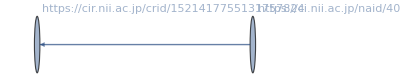
{20231120,{36,1},-Graphics-}

```mathematica
storyGrIdxFlDs[4][[200]]
```

4. 不要と思われるvertexを削除(1)：

```mathematica
(storyGrIdxFlDsVD1[4]=Map[{#[[1]],#[[2]],If[VertexQ[#[[3]],"-"],VertexDelete[#[[3]],"-"],#[[3]]]}&,storyGrIdxFlDs[4]])//Dimensions
```

{226221,3}

5. 不要と思われるvertexを削除(2)：

rm候補のパターン：

```mathematica
rmpattAll=.
```

```mathematica
rmpattAll[4]={rmpatt[4][1]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/static.*"],
rmpatt[4][2]=RegularExpression["https://jdcat.jsps.go.jp/api.*"],
rmpatt[4][3]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*"],
rmpatt[4][4]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*"],
rmpatt[4][5]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/img.*"],
rmpatt[4][6]=RegularExpression["https://.*/.*\\.svg"],
rmpatt[4][7]=RegularExpression["https://.*/.*\\.js"],
rmpatt[4][8]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/.*\\.js\\?.*"],
rmpatt[4][9]=RegularExpression["https://jdcat.jsps.go.jp/.*\\.js\\?.*"],
rmpatt[4][10]=RegularExpression["https://.*/.*\\.woff2.*"],
rmpatt[4][11]=RegularExpression["https://.*/.*\\.css"],
rmpatt[4][12]=RegularExpression["https://.*/css/.*"],
rmpatt[4][13]=RegularExpression["https://.*/.*\\.favicon.ico"],
rmpatt[4][14]="https://jdcat.jsps.go.jp/get_search_setting",
rmpatt[4][15]="https://jdcat.jsps.go.jp/facet-search/get-title-and-order"
}
```

{RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*],RegularExpression[https://jdcat.jsps.go.jp/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/img.*],RegularExpression[https://.*/.*\.svg],RegularExpression[https://.*/.*\.js],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/.*\.js\?.*],RegularExpression[https://jdcat.jsps.go.jp/.*\.js\?.*],RegularExpression[https://.*/.*\.woff2.*],RegularExpression[https://.*/.*\.css],RegularExpression[https://.*/css/.*],RegularExpression[https://.*/.*\.favicon.ico],https://jdcat.jsps.go.jp/get_search_setting,https://jdcat.jsps.go.jp/facet-search/get-title-and-order}

rm候補のパターンから削除頂点リストを生成（参考）：

```mathematica
createRmList[gr_,rmpatt_]:=Module[{vlist},
vlist=VertexList[gr];
Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]]
]
```

rm候補のパターンを指定してグラフからマッチする頂点を削除する関数：

```mathematica
rmV[gr_,rmpatt_]:=Module[{vlist,pathlist},
vlist=VertexList[gr];
pathlist=Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]];
VertexDelete[gr,pathlist]
]
```

```mathematica
(storyGrIdxFlDsVD2[4]=Map[{#[[1]],#[[2]],rmV[#[[3]],rmpattAll[4]]}&,storyGrIdxFlDsVD1[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[If[StringTake[,1]==/,pathhead$21351<>epath$21351,epath$21351],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[If[StringTake[,1]==/,pathhead$21351<>epath$21351,epath$21351],RegularExpression[https://jdcat.jsps.go.jp/api.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[If[StringTake[,1]==/,pathhead$21351<>epath$21351,epath$21351],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{226221,3}

6. 以上の操作により不正となったグラフを削除(対象をpick)：

ノード数 >= 2：

```mathematica
pickPos[4][1]=Flatten[Position[Map[VertexCount[#[[3]]]&,storyGrIdxFlDsVD2[4]],x_/;x>=2]];
```

```mathematica
(storyGrIdxFlDs2[4]=storyGrIdxFlDsVD2[4][[pickPos[4][1]]])//Dimensions
```

{200882,3}

エッジ数 >= 1：

```mathematica
pickPos[4][2]=Flatten[Position[Map[EdgeCount[#[[3]]]&,storyGrIdxFlDs2[4]],x_/;x>=1]];
```

```mathematica
(storyGrIdxFlDs3[4]=storyGrIdxFlDs2[4][[pickPos[4][2]]])//Dimensions
```

{186165,3}

上が分離されたストーリー

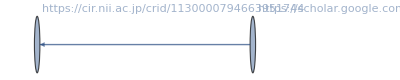
{20231120,{1,1},-Graphics-}

```mathematica
storyGrIdxFlDs3[4][[1]]
```

#### Pre Op 2.1.1 : save

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story

```mathematica
SetDirectory[savedir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story

```mathematica
Directory[]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story

```mathematica
Timing[Save["storyGrIdxFlDs3.save",storyGrIdxFlDs3]]
Timing[Save["storyGrIdxFlDs3.save",toCRID]]
Timing[Save["ckan.save",ckanName]]
Timing[Save["ckan.save",ckanCridAC]]
Timing[Save["ckan.save",ckanCridPLogPosAC]]
Timing[Save["ckan.save",ckanCridRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRACQ]]
```

{27.8413,Null}

{0.000293,Null}

{0.203791,Null}

{0.549108,Null}

{0.000627,Null}

{0.000296,Null}

{0.000577,Null}

{0.000744,Null}

<<< Saveデータを読んだ時はここまで飛ばす。 >>>

#### Pre Op 2.2

Saveデータがある時は読み込む：

```mathematica
SetDirectory["/Volumes/elecom/NII/togo-log/rcoslogs/log/D="<>date<>"/"<>base["all"]<>"/_story"]
```

SetDirectory::cdir: Cannot set current directory to /Volumes/elecom/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story.

$Failed

```mathematica
Timing[Get["storyGrIdxFlDs.save"];]
```

Get::noopen: Cannot open storyGrIdxFlDs.save.

{0.008672,Null}

## Analysis

### Analysis 1 graph property

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{186165}

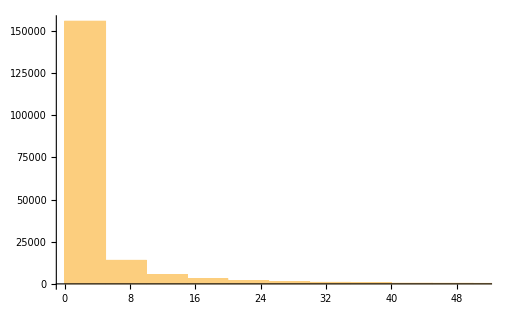

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{186165}

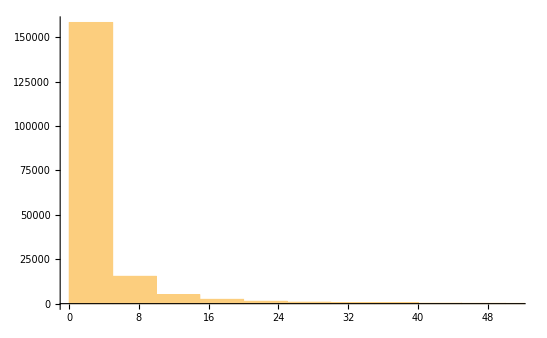

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{186165}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{186165}

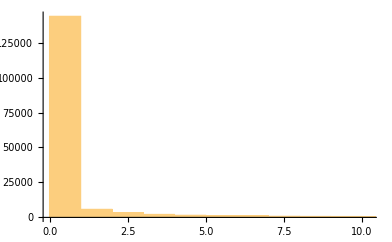

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{186165}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{186165}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{186165}

### Analysis 2 base interaction

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {cir.nii.ac.jp} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{186165}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{34,40,41,58,61,72,77,103,161,162,166,167,169,181,197,227,228,229,231,232,233,234,235,245,312,332,333,397,401,436,452,460,622,666,730,732,836,882,885,1130,1152,1153,1155,1206,1522,1631}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:binder.cs.rcos.nii.ac.jp,http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:grafana.cs.rcos.nii.ac.jp,http:harbor.cs.rcos.nii.ac.jp,http:jdcat.jsps.go.jp,http:jupyter.cs.rcos.nii.ac.jp,http:lms.nii.ac.jp,https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com,https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com:443,https:analytics.la.lms.nii.ac.jp,https:analytics.la.test.lms.nii.ac.jp,https:api.ci.nii.ac.jp,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:ci-nii-ac-jp.cdn.ampproject.org,https:cir.nii.ac.jp,https:cir-nii-ac-jp.bukkyo.idm.oclc.org,https:cir-nii-ac-jp.nanzan-u.idm.oclc.org,https:cir-nii-ac-jp.swu.idm.oclc.org,https:cir-nii-ac-jp.translate.goog,https:core.orthros.gakunin.nii.ac.jp,https:fukuoka-u.repo.nii.ac.jp,https:ge.nii.ac.jp,https:ge.nii.ac.jp:443,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jdcat.jsps.go.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:lms.nii.ac.jp,https:meatwiki.nii.ac.jp,https:niph.repo.nii.ac.jp,https:niu.repo.nii.ac.jp,https:openidp.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:support.nii.ac.jp,https:tohoku.repo.nii.ac.jp,https:tohtech.repo.nii.ac.jp,https:tokoha-u.repo.nii.ac.jp,https:webfront2.nii.ac.jp:443,https:www.nii.ac.jp,https:www.unii.ac.jp}

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{186165}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,164123},{1,22038},{3,4}}

```mathematica
(GrBasesTly[4]=Tally[GrBases[4]])//Dimensions
```

{1800,2}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,145587},{2,40571},{0,7}}

```mathematica
(GrNiiBasesTly[4]=Tally[GrNiiBases[4]])//Dimensions
```

{54,2}

```mathematica
GrNiiBasesTly[4]//TableForm
```

https:cir.nii.ac.jp | 145372
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 20274
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 19934
https:cir.nii.ac.jp
https:support.nii.ac.jp | 127
http:harbor.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:jdcat.jsps.go.jp | 38
https:cir.nii.ac.jp
https:www.nii.ac.jp | 5
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 72
https:jupyter.cs.rcos.nii.ac.jp | 70
https:cir.nii.ac.jp
https:www.unii.ac.jp | 14
https:lms.nii.ac.jp | 107
http:jdcat.jsps.go.jp
https:jdcat.jsps.go.jp | 1
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 46
https:lms.nii.ac.jp
https:www.nii.ac.jp | 1
https:jdcat.jsps.go.jp
https:support.nii.ac.jp | 1
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 5
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp | 3
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 3
https:cir.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 3
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 4
https:cir.nii.ac.jp
https:fukuoka-u.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:cir-nii-ac-jp.swu.idm.oclc.org | 3
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 7
http:grafana.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 10
https:cir.nii.ac.jp
https:cir-nii-ac-jp.nanzan-u.idm.oclc.org | 3
https:idp.nii.ac.jp
https:lms.nii.ac.jp | 1
https:core.orthros.gakunin.nii.ac.jp
https:lms.nii.ac.jp | 1
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 7
https:cir.nii.ac.jp
https:tohtech.repo.nii.ac.jp | 1
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 5
https:cir.nii.ac.jp
https:cir-nii-ac-jp.translate.goog | 2
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 8
http:jupyter.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:tohoku.repo.nii.ac.jp | 1
https:lms.nii.ac.jp
https:meatwiki.nii.ac.jp | 1
https:cir.nii.ac.jp
https:cir-nii-ac-jp.bukkyo.idm.oclc.org | 1
 | 7
https:cir.nii.ac.jp
https:niph.repo.nii.ac.jp | 1
https:jdcat.jsps.go.jp
https:www.nii.ac.jp | 1
https:analytics.la.lms.nii.ac.jp
https:lms.nii.ac.jp | 6
https:analytics.la.test.lms.nii.ac.jp
https:lms.nii.ac.jp | 1
https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com:443
https:cir.nii.ac.jp | 1
https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com
https:cir.nii.ac.jp | 1
http:lms.nii.ac.jp
https:lms.nii.ac.jp | 2
http:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:ci-nii-ac-jp.cdn.ampproject.org
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp:443 | 1
https:cir.nii.ac.jp
https:tokoha-u.repo.nii.ac.jp | 1
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:api.ci.nii.ac.jp
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:niu.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 1
https:cir.nii.ac.jp
https:webfront2.nii.ac.jp:443 | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

### Analysis 3 time series

```mathematica
accessFirst=(Cases[accessTime[4],x_/;x>0]//Min)
```

3.90943×10^9

```mathematica
accessLast=(Cases[accessTime[4],x_/;x>0]//Max)
```

3.90951×10^9

```mathematica
Sort[accessTime["ci"]]//Length
```

2557038

```mathematica
BC600["ci"]=BinCounts[Sort[accessTime["ci"]],{accessFirst,accessLast,60*10}]
```

{15641,15400,14930,17957,17538,16736,16633,18048,17053,17045,19571,14858,17031,14912,12885,14700,14827,19503,17447,16164,14510,11866,10697,10259,12226,11674,12400,13942,11974,14300,11507,12327,11585,12235,13559,11868,9616,12919,14456,12646,14017,14760,13279,14891,11322,12413,14399,14230,12790,14020,12749,11245,11892,14435,14650,17372,16077,16478,15665,15796,14441,15398,16139,15649,17087,16308,16112,19271,19844,19842,19628,17004,15687,14906,14706,15601,17537,16595,17176,18400,17677,19190,21139,23122,20992,23251,21989,21082,24144,20845,20141,21648,24282,23536,24762,22934,20558,22629,23352,23309,24082,23870,23467,23131,20671,19542,21954,18599,17608,20921,22195,18824,20949,20980,19504,21505,19761,20354,21180,20752,20938,20587,19797,21318,20327,17673,18645,19109,19912,20250,20035,21223,21739,21954,20465,20884,20491,21812,20432,22276,22955,22605,22735}

```mathematica
BC600["cs"]=BinCounts[Sort[accessTime["cs"]],{accessFirst,accessLast,60*10}]
```

{1,33,17,26,70,2,12,31,19,3,1,2,5,9,24,2,58,1,2,2,4708,141,6,2,0,1,19,1,59,2,0,0,17,1,0,1,1,2,23,1,58,1,2,0,17,1,2,2,0,0,17,85,60,101,70,16,36,4,1,5,444,0,97,6,428,156,109,121,133,111,226,115,85,44,60,39,98,64,197,652,480,452,934,505,267,243,118,72,236,116,320,176,272,353,128,228,42,7,48,5,91,13,195,196,651,382,273,406,448,18,483,13,66,59,2,3,17,0,2,2,2,2,18,1,60,12,5,0,23,0,6,3,12,3,29,3,62,0,4,1,17,3,0}

```mathematica
BC600["la"]=BinCounts[Sort[accessTime["la"]],{accessFirst,accessLast,60*10}]
```

{2,2,7,0,5,0,74,16,0,0,42,1,1,3,0,3,0,0,1,0,0,45,221,2,57,158,39,1,8,0,2,1,0,8,4,1,0,2,0,2,1,0,26,2,0,12,3,1,0,0,8,8,5,21,0,6,8,3,4,72,36,2,50,63,1,3,127,382,708,733,244,45,37,73,511,288,155,25,39,51,145,67,142,31,3,31,45,82,108,54,2,29,2,1,1,41,118,0,6,1,12,99,130,1,22,6,29,26,2,14,2,7,8,4,2,50,2,6,63,34,8,6,2,3,2,22,4,2,6,7,8,5,2,5,4,31,101,108,4,10,2,3,16}

```mathematica
BC600["wk"]=BinCounts[Sort[accessTime["wk"]],{accessFirst,accessLast,60*10}]
```

{38,47,74,46,11,2,13,18,17,0,10,4,27,20,28,26,23,14,27,52,43,45,48,40,36,38,36,36,38,58,23,11,31,70,51,53,28,45,63,42,40,13,47,43,48,42,44,12,42,40,54,64,19,7,53,54,43,70,74,30,62,34,28,22,34,61,50,39,62,43,71,41,39,38,53,38,40,40,34,36,45,69,77,56,48,43,54,43,71,58,67,115,231,82,42,23,33,44,45,42,55,25,38,50,55,55,57,12,66,53,62,57,126,207,65,34,58,47,56,39,25,42,75,68,47,35,45,49,37,36,51,21,52,51,1,45,50,29,12,29,35,48,36}

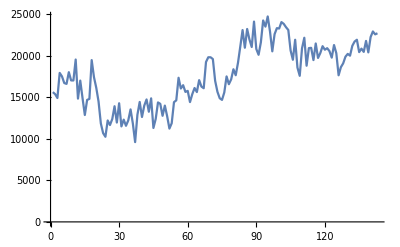

```mathematica
ListPlot[BC600["ci"],PlotRange->Full,Joined->True]
```

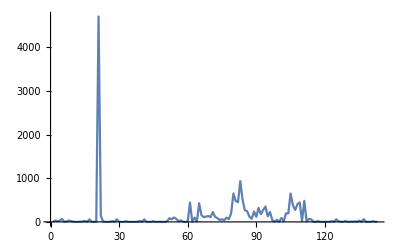

```mathematica
ListPlot[BC600["cs"],PlotRange->Full,Joined->True]
```

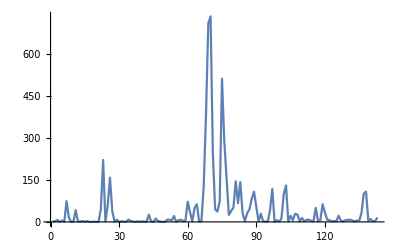

```mathematica
ListPlot[BC600["la"],PlotRange->Full,Joined->True]
```

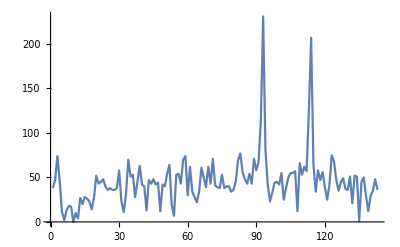

```mathematica
ListPlot[BC600["wk"],PlotRange->Full,Joined->True]
```

### Analysis 4 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{186165}

```mathematica
ckanGrP[4][[2]]
```

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{186165}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{186165}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{99,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{17,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{101,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{101,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{2,8,14,2,5,14,34,2,2,2,2,2,93,92,93,37,21,43,105,14,9,2,13,26,10,20,2,19,35,269,265,265,41,46,67,6,31,18,18,25,11,12,12,6,8,13,26,14,14,17,45,2,27,41,45,7,22,12,14,16,24,8,18,68,72,69,65,423,423,462,423,423,426,423,11,17,94,99,95,62,14,2,23,4,2,25,6,29,16,23,36,36,36,9,7,18,11,3,6,1099,17}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{0.,181.,236.,0.,62.,10090.,29306.,0.,0.,0.,0.,0.,19258.,19246.,19246.,2084.,16014.,4963.,35597.,1652.,779.,0.,1471.,1522.,7197.,3292.,0.,3870.,3960.,12997.,3326.,3326.,17575.,29621.,30254.,38.,28696.,8609.,8648.,5124.,2778.,698.,145.,154.,218.,13946.,14936.,13946.,746.,547.,80409.,0.,27159.,14603.,5688.,103.,15398.,1778.,2091.,11978.,13402.,17069.,12300.,18443.,28412.,22531.,18443.,33342.,33342.,41975.,33342.,34501.,33342.,33342.,1610.,13257.,26838.,26826.,26826.,4057.,1811.,0.,6275.,22.,0.,12197.,10232.,3259.,7351.,736.,1259.,1222.,1222.,196.,177.,620.,1537.,5.,25958.,86309.,1379.}

### Analysis 5 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{101,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{1573,1},{7088,1},{8561,1},{11060,1},{15038,1},{19369,1},{19523,1},{21370,1},{21376,1},{21473,1},{21689,1},{28729,1},{28985,1},{28985,1},{28985,1},{29113,1},{29234,1},{29989,1},{33554,1},{36594,1},{37594,1},{42418,1},{43890,1},{48565,1},{49170,1},{49733,1},{51268,1},{51701,1},{56865,1},{59808,1},{59808,1},{59808,1},{62885,1},{63160,1},{63160,1},{64191,1},{64540,1},{64540,1},{64540,1},{72164,1},{72525,1},{74616,1},{75978,1},{81946,1},{85006,1},{85040,1},{85040,1},{85040,1},{94427,1},{99062,1},{99527,1},{101752,1},{101976,1},{102058,1},{102058,1},{103687,1},{104234,1},{104542,1},{104542,1},{104543,1},{104543,1},{104547,1},{104723,1},{105495,1},{105495,1},{105495,1},{105495,1},{105656,1},{105656,1},{105656,1},{105656,1},{105656,1},{105656,1},{105656,1},{105818,1},{105995,1},{106034,1},{106034,1},{106034,1},{107502,1},{110157,1},{110834,1},{111835,1},{112128,1},{113311,1},{114850,1},{118446,1},{119111,1},{119138,1},{120490,1},{121384,1},{121384,1},{121384,1},{124291,1},{126931,1},{140074,1},{142827,1},{147026,1},{155593,1},{159924,1},{163957,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{2,8,14,2,5,14,34,2,2,2,2,2,93,92,93,37,21,43,105,14,9,2,13,26,10,20,2,19,35,269,265,265,41,46,67,6,31,18,18,25,11,12,12,6,8,13,26,14,14,17,45,2,27,41,45,7,22,12,14,16,24,8,18,68,72,69,65,423,423,462,423,423,426,423,11,17,94,99,95,62,14,2,23,4,2,25,6,29,16,23,36,36,36,9,7,18,11,3,6,1099,17}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{1,14,28,1,5,15,59,1,1,1,1,1,153,140,150,55,42,63,148,15,12,1,17,52,13,42,1,32,75,667,512,513,56,83,111,5,43,22,23,29,13,14,19,6,8,15,34,16,17,23,68,1,37,76,81,12,30,13,16,25,40,9,22,92,108,98,94,650,652,743,652,656,657,652,26,45,265,269,267,100,20,1,27,4,1,64,5,87,18,35,50,48,49,14,7,37,15,2,5,1373,22}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{101}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{0,0.716667,1.03333,0,0.433333,86.7333,464.733,0,0,0,0,0,64.7833,72.8333,72.8333,11.2833,243.067,67.05,351.3,7.96667,7.68333,0,15.95,16.8,73.05,19.5833,0,21.1167,37.7833,107.017,7.48333,7.48333,151.6,273.583,344.167,0.3,171.733,128.767,128.767,37.0667,37.55,8.03333,0.416667,2.05,1.78333,228.283,175.817,227.85,4.78333,6.01667,1107.65,0,160.133,139.1,54.85,0.65,157.65,26.65,26.4667,99.0333,98.8167,280.433,192.583,88.9167,107.2,168.25,168.25,67.6,67.6,94.25,67.6,67.6,67.6,67.6,11.4667,100.233,118.8,118.8,118.717,10.8667,6.05,0,89.9167,0.2,0,120.667,134.833,7.85,61.5333,2.63333,4.81667,4.81667,4.81667,2.15,1.06667,2.08333,15.2667,0.0833333,240.6,26.95,13.7667}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{0.,181.,236.,0.,62.,10090.,29306.,0.,0.,0.,0.,0.,19258.,19246.,19246.,2084.,16014.,4963.,35597.,1652.,779.,0.,1471.,1522.,7197.,3292.,0.,3870.,3960.,12997.,3326.,3326.,17575.,29621.,30254.,38.,28696.,8609.,8648.,5124.,2778.,698.,145.,154.,218.,13946.,14936.,13946.,746.,547.,80409.,0.,27159.,14603.,5688.,103.,15398.,1778.,2091.,11978.,13402.,17069.,12300.,18443.,28412.,22531.,18443.,33342.,33342.,41975.,33342.,34501.,33342.,33342.,1610.,13257.,26838.,26826.,26826.,4057.,1811.,0.,6275.,22.,0.,12197.,10232.,3259.,7351.,736.,1259.,1222.,1222.,196.,177.,620.,1537.,5.,25958.,86309.,1379.}

```mathematica
staytimeCKAN/60
```

{0.,3.01667,3.93333,0.,1.03333,168.167,488.433,0.,0.,0.,0.,0.,320.967,320.767,320.767,34.7333,266.9,82.7167,593.283,27.5333,12.9833,0.,24.5167,25.3667,119.95,54.8667,0.,64.5,66.,216.617,55.4333,55.4333,292.917,493.683,504.233,0.633333,478.267,143.483,144.133,85.4,46.3,11.6333,2.41667,2.56667,3.63333,232.433,248.933,232.433,12.4333,9.11667,1340.15,0.,452.65,243.383,94.8,1.71667,256.633,29.6333,34.85,199.633,223.367,284.483,205.,307.383,473.533,375.517,307.383,555.7,555.7,699.583,555.7,575.017,555.7,555.7,26.8333,220.95,447.3,447.1,447.1,67.6167,30.1833,0.,104.583,0.366667,0.,203.283,170.533,54.3167,122.517,12.2667,20.9833,20.3667,20.3667,3.26667,2.95,10.3333,25.6167,0.0833333,432.633,1438.48,22.9833}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/url?q=https://cir.nii.ac.jp/&sa=U&sqi=2&ved=2ahUKEwihwqOM0dGCAxVGNN4KHW73BGMQFnoECAcQAQ&usg=AOvVaw1TP0cPw4owrZdTH0aWcRIf⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.google.com/url?q=https://cir.nii.ac.jp/&sa=U&sqi=2&ved=2ahUKEwiaq_TUkNKCAxUPsFYBHRnID74QFnoECAUQAQ&usg=AOvVaw3bwiI2wZC5Md_ZZTpkmgcf⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{101}

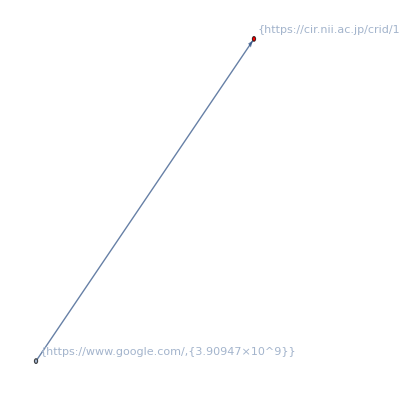
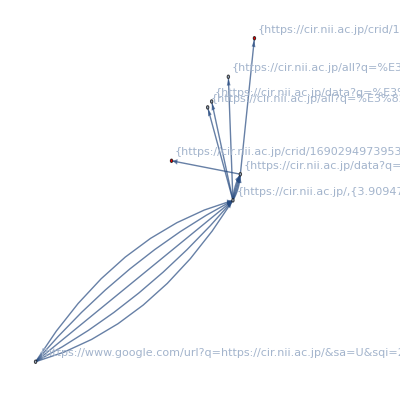
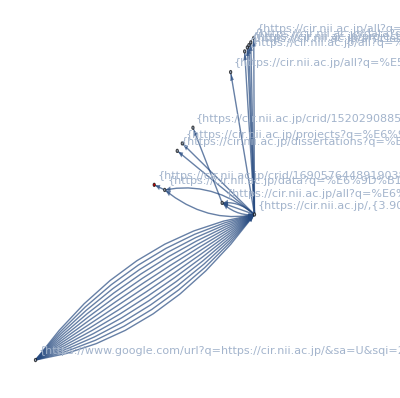
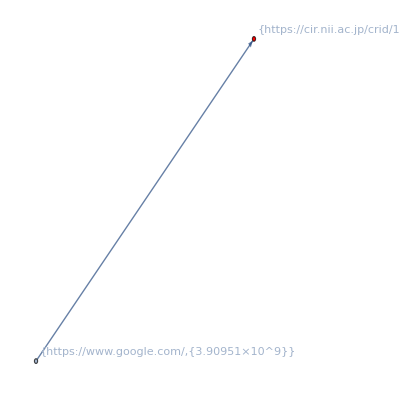
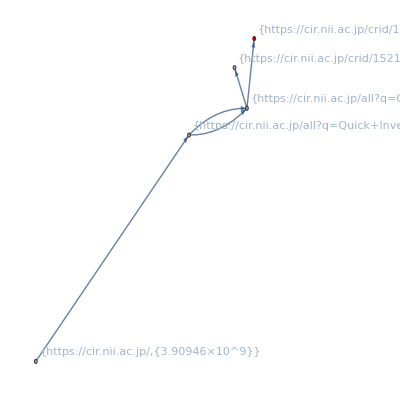
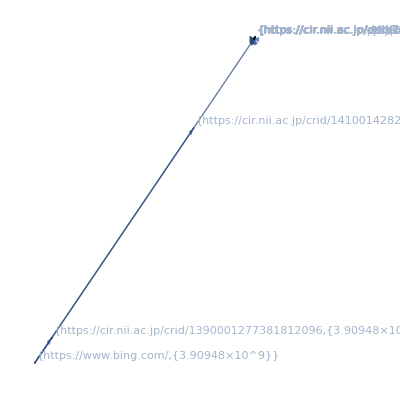
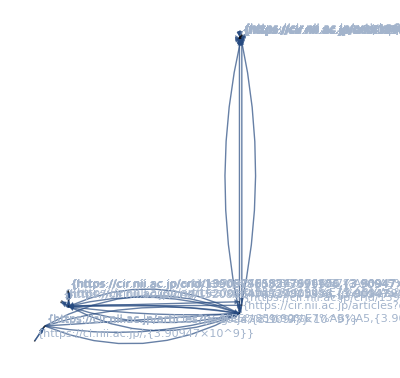
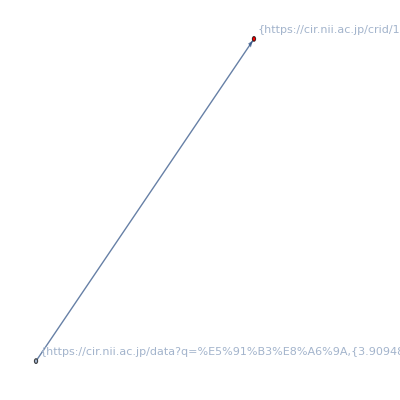
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
ckanGrPRselHLTL[4]//TableForm
```

### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLog[4]//Length}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 22645372
2587383

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 188
25
213 | 159
14
159

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 186165
101

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96
97
98
99
100
101 | 1573 | 1
7088 | 1
8561 | 1
11060 | 1
15038 | 1
19369 | 1
19523 | 1
21370 | 1
21376 | 1
21473 | 1
21689 | 1
28729 | 1
28985 | 1
28985 | 1
28985 | 1
29113 | 1
29234 | 1
29989 | 1
33554 | 1
36594 | 1
37594 | 1
42418 | 1
43890 | 1
48565 | 1
49170 | 1
49733 | 1
51268 | 1
51701 | 1
56865 | 1
59808 | 1
59808 | 1
59808 | 1
62885 | 1
63160 | 1
63160 | 1
64191 | 1
64540 | 1
64540 | 1
64540 | 1
72164 | 1
72525 | 1
74616 | 1
75978 | 1
81946 | 1
85006 | 1
85040 | 1
85040 | 1
85040 | 1
94427 | 1
99062 | 1
99527 | 1
101752 | 1
101976 | 1
102058 | 1
102058 | 1
103687 | 1
104234 | 1
104542 | 1
104542 | 1
104543 | 1
104543 | 1
104547 | 1
104723 | 1
105495 | 1
105495 | 1
105495 | 1
105495 | 1
105656 | 1
105656 | 1
105656 | 1
105656 | 1
105656 | 1
105656 | 1
105656 | 1
105818 | 1
105995 | 1
106034 | 1
106034 | 1
106034 | 1
107502 | 1
110157 | 1
110834 | 1
111835 | 1
112128 | 1
113311 | 1
114850 | 1
118446 | 1
119111 | 1
119138 | 1
120490 | 1
121384 | 1
121384 | 1
121384 | 1
124291 | 1
126931 | 1
140074 | 1
142827 | 1
147026 | 1
155593 | 1
159924 | 1
163957 | 1 | 2
8
14
2
5
14
34
2
2
2
2
2
93
92
93
37
21
43
105
14
9
2
13
26
10
20
2
19
35
269
265
265
41
46
67
6
31
18
18
25
11
12
12
6
8
13
26
14
14
17
45
2
27
41
45
7
22
12
14
16
24
8
18
68
72
69
65
423
423
462
423
423
426
423
11
17
94
99
95
62
14
2
23
4
2
25
6
29
16
23
36
36
36
9
7
18
11
3
6
1099
17 | 1
14
28
1
5
15
59
1
1
1
1
1
153
140
150
55
42
63
148
15
12
1
17
52
13
42
1
32
75
667
512
513
56
83
111
5
43
22
23
29
13
14
19
6
8
15
34
16
17
23
68
1
37
76
81
12
30
13
16
25
40
9
22
92
108
98
94
650
652
743
652
656
657
652
26
45
265
269
267
100
20
1
27
4
1
64
5
87
18
35
50
48
49
14
7
37
15
2
5
1373
22 | 0
0.716667
1.03333
0
0.433333
86.7333
464.733
0
0
0
0
0
64.7833
72.8333
72.8333
11.2833
243.067
67.05
351.3
7.96667
7.68333
0
15.95
16.8
73.05
19.5833
0
21.1167
37.7833
107.017
7.48333
7.48333
151.6
273.583
344.167
0.3
171.733
128.767
128.767
37.0667
37.55
8.03333
0.416667
2.05
1.78333
228.283
175.817
227.85
4.78333
6.01667
1107.65
0
160.133
139.1
54.85
0.65
157.65
26.65
26.4667
99.0333
98.8167
280.433
192.583
88.9167
107.2
168.25
168.25
67.6
67.6
94.25
67.6
67.6
67.6
67.6
11.4667
100.233
118.8
118.8
118.717
10.8667
6.05
0
89.9167
0.2
0
120.667
134.833
7.85
61.5333
2.63333
4.81667
4.81667
4.81667
2.15
1.06667
2.08333
15.2667
0.0833333
240.6
26.95
13.7667 | 0.
3.01667
3.93333
0.
1.03333
168.167
488.433
0.
0.
0.
0.
0.
320.967
320.767
320.767
34.7333
266.9
82.7167
593.283
27.5333
12.9833
0.
24.5167
25.3667
119.95
54.8667
0.
64.5
66.
216.617
55.4333
55.4333
292.917
493.683
504.233
0.633333
478.267
143.483
144.133
85.4
46.3
11.6333
2.41667
2.56667
3.63333
232.433
248.933
232.433
12.4333
9.11667
1340.15
0.
452.65
243.383
94.8
1.71667
256.633
29.6333
34.85
199.633
223.367
284.483
205.
307.383
473.533
375.517
307.383
555.7
555.7
699.583
555.7
575.017
555.7
555.7
26.8333
220.95
447.3
447.1
447.1
67.6167
30.1833
0.
104.583
0.366667
0.
203.283
170.533
54.3167
122.517
12.2667
20.9833
20.3667
20.3667
3.26667
2.95
10.3333
25.6167
0.0833333
432.633
1438.48
22.9833

### Export:CKAN impact

エクスポート用：

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{101}

```mathematica
(ckanELX=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}])//Dimensions
```

{101}

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231120/T=4/_story

```mathematica
(*Export["ckanedgelist.json",ckanELX]*)
```

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.909940924989612×10^9

```mathematica
end-start
```

829.846626